## Setting Up Equations

```mathematica
Clear["Global`*"]
```

## Solving for RISSOMIN and RISSOPLUS

```mathematica
<<KerrGeodesics`
```

## Range check for possible ISSO’s

```mathematica
a = 0.7;
Subscript[χ, inc] = Cos[π/4];
RI = KerrGeoISSO[a,Subscript[χ, inc]];
L = KerrGeoAngularMomentum[a,KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ];
Q = KerrGeoCarterConstant[a,KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ];
ϵ =KerrGeoEnergy[a, KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ];
```

```mathematica
(*RI=7.4;*)
Manipulate[Subscript[χ, inc] = Cos[θ];
RI = KerrGeoISSO[a,Subscript[χ, inc]];
L = KerrGeoAngularMomentum[a,KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ];
Q = KerrGeoCarterConstant[a,KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ];
ϵ =KerrGeoEnergy[a, KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ];
	
J = 1-ϵ^2;
R4 =(a^2 Q)/(J*RI^3) ;
Z1=Sqrt[1/2 (1+(L^2+Q)/(a^2 (1-ϵ^2))-√(-(4 Q)/(a^2 (1-ϵ^2))+(-1-(L^2+Q)/(a^2 (1-ϵ^2)))^2))];
Z2 =Sqrt[ (a^2(1-ϵ^2))/2 (1+(L^2+Q)/(a^2 (1-ϵ^2))+√(-(4 Q)/(a^2 (1-ϵ^2))+(-1-(L^2+Q)/(a^2 (1-ϵ^2)))^2))];
KZ = a^2*J(Z1^2/Z2^2);

Λ = z[(4 EllipticK[KZ])/Z2];
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);
CoordTimeAveRadialInFlow[r_]:= (-Sqrt[R[r]]Λ)/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )+1/((4 EllipticK[KZ])/Z2)(Tz[Mino[r]+(4 EllipticK[KZ])/Z2] - Tz[Mino[r]] ));


Plot[CoordTimeAveRadialInFlow[r], {r,RP,RI}, PlotLabel->L, PlotRange->All, MaxRecursion->10],{RI,6-0.5,6+0.5 }]
```

4.60707

### λ of R equation

```mathematica
Mino[r_]:=(2 √(r-R4))/(√(J (RI-r) (R4-RI)^2));
(*Solve[-3 R+3 R ϵ^2-(3 a^2 Q)/(R (1-ϵ^2))+(3 a^2 Q ϵ^2)/(R (1-ϵ^2))==-a^2-Q+4 a ϵ+2 a^2 ϵ^2-(2+a ϵ)^2,R];*)
```

### Radial Equation

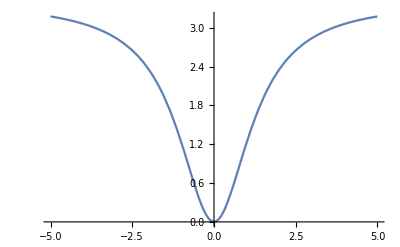

```mathematica
r[λ_]:=((RI(RI-R4)^2 J*(λ)^2+4*R4)/((RI-R4)^2 J*(λ)^2+4));
Plot[r[λ],{λ,-5,5}]
```

0.993602

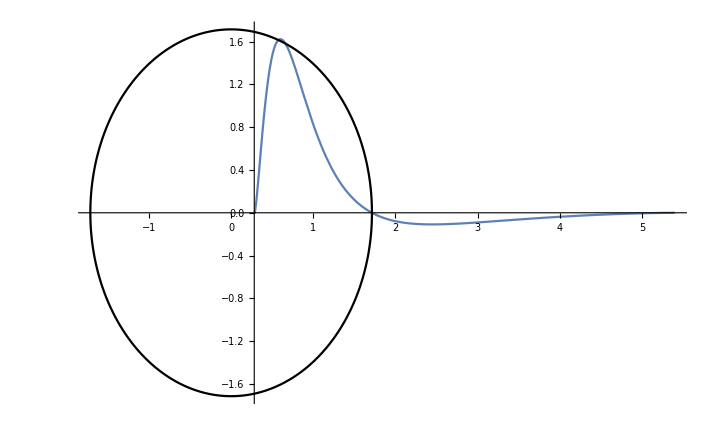

```mathematica
Λ = z[(4 EllipticK[KZ])/Z2]
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)
CoordTimeAveRadialInFlow[r_]:= (-Sqrt[R[r]]Λ)/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )+1/((4 EllipticK[KZ])/Z2)(Tz[Mino[r]+(4 EllipticK[KZ])/Z2] - Tz[Mino[r]] ))
P2 =ParametricPlot[{RP*Sin[u],RP*Cos[u] },{u,-π,π},PlotStyle->{Opacity[1],Black,Specularity[White,10]},Axes->None,Mesh->None,PlotRange->All];

P1 = Plot[CoordTimeAveRadialInFlow[r], {r,RI,0}, PlotRange->All];
Show[P1,P2]
```

π/2

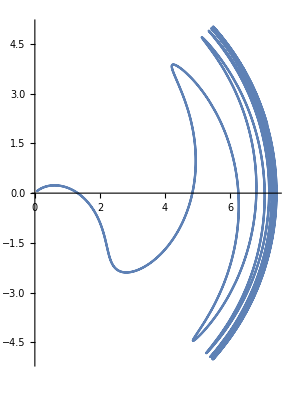

```mathematica
θ0 =π/2 
ΥZ = (π*Z2)/(2*EllipticK[KZ]);
qZ[λ_]:= ΥZ*λ 
z[λ_] :=Z1*JacobiSN[Z2*(λ  ) + EllipticK[KZ],KZ];
θ[λ_] := ArcCos[Z1*JacobiSN[Z2*(λ ) + EllipticK[KZ],KZ]];
PolyZ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
ParametricPlot[{r[λ]*Cos[π/2-θ[λ]],r[λ]*Sin[π/2-θ[λ]]} , {λ,-10,10}, PlotRange->All]
```

```mathematica
z[(4 EllipticK[KZ])/Z2]
```

0.675061

```mathematica
z[λ_] :=Z1*JacobiSN[Z2*(λ  ) + EllipticK[KZ],KZ];;

Manipulate[Plot[{z[λ],z[λ+n*4*EllipticK[KZ]/Z2],z[λ]-z[λ+n*4*EllipticK[KZ]/Z2],n},{λ,-2,2}],{n,0,10}]

 EllipticK[Sqrt[1-KZ^2]]
 EllipticK[KZ]
```

```mathematica
Tz[λ_]:=1/J ϵ  (-Z2 EllipticE[JacobiAmplitude[Z2 (λ  ) + EllipticK[KZ],KZ],KZ]+(Z2-a^2 J/Z2) EllipticF[JacobiAmplitude[Z2 (λ  ) + EllipticK[KZ],KZ],KZ])
T[λ_]:= Trr[λ]+Tz[λ]+a*L*λ
```

```mathematica
Λ = z[(4 EllipticK[KZ])/Z2]
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)
CoordTimeAveRadialInFlow[r_]:= (-Sqrt[R[r]]Λ)/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )+1/((4 EllipticK[KZ])/Z2)(Tz[Mino[r]+(4 EllipticK[KZ])/Z2] - Tz[Mino[r]] ))
P2 =ParametricPlot[{RP*Sin[u],RP*Cos[u] },{u,-π,π},PlotStyle->{Opacity[1],Black,Specularity[White,10]},Axes->None,Mesh->None,PlotRange->All];

P1 = Plot[CoordTimeAveRadialInFlow[r], {r,RI,0}, PlotRange->All];
Show[P1,P2]
```